# Ex 1

Q1: Write the expression f(x)= x e^-x + x (1 - x), and evaluate it at the points x=0, 0.1, 0.2, 0.4, 0.8.

```mathematica
f[x_]:=x*Exp[-x]+x(1-x)
```

```mathematica
f[0]
f@0.1
0.2//f
f[0.4]
f[0.8]
```

0

0.180484

0.323746

0.508128

0.519463

Q2: Find the first three roots of the Bessel function J_1(x). Hint: The Bessel function in Mathematica is BesselJ[n, x]. It may also be useful to plot the function.

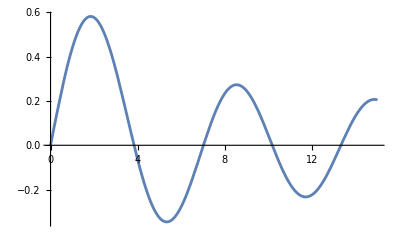

```mathematica
Plot[BesselJ[1,x], {x, 0, 15}]
```

```mathematica
FindRoot[BesselJ[1,x]==0, {x, 4}]
```

{x→3.83171}

```mathematica
FindRoot[BesselJ[1,x]==0, {x, 7}]
```

{x→7.01559}

```mathematica
FindRoot[BesselJ[1,x]==0, {x, 10}]
```

{x→10.1735}

```mathematica
FindRoot[BesselJ[1,x]==0, {x, {4, 7, 10}}]
```

{x→{3.83171,7.01559,10.1735}}

Q3: Integrate the expression f(x) = sin(x) e^-x, and then take it’s derivative.

```mathematica
f[x_]:=Sin[x]Exp[-x]
```

```mathematica
Integrate[f[x], x]
```

ⅇ^-x Sin (-1-x)

```mathematica
D[%,x]
```

-ⅇ^-x Sin-ⅇ^-x Sin (-1-x)

```mathematica
Simplify[%]
```

ⅇ^-x Sin x